```mathematica
fMS[kappa_,theta_]:=Exp[kappa*Cos[theta]^2]
```

```mathematica
Integrate[fMS[kappa,theta]*Sin[theta],{theta,0,Pi}]
```

(√π Erfi[√kappa])/(√kappa)

```mathematica
IMS[kappa_,psi_]:=Integrate[fMS[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2},Assumptions->psi≥0 && psi≤Pi/2]
```

```mathematica
IMS[kappa,psi]
```

ConditionalExpression[(ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 √kappa),psi>0&&2 psi<π]

```mathematica
FullSimplify[(ⅇ^(kappa Cos[psi]^2) √π Erf[√kappa Cos[psi]] Sec[psi])/(2 √kappa)/((√π Erfi[√kappa])/(√kappa))]
```

(ⅇ^(kappa Cos[psi]^2) Erf[√kappa Cos[psi]] Sec[psi])/(2 Erfi[√kappa])

```mathematica
IMScorr[kappa_,psi_]:=Integrate[fMS[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
IMScorr[kappa_,psi_]
```

∫_psi_^(π/2) (ⅇ^(Cos[theta]^2 kappa_) √kappa_ Sec[psi_] Tan[theta])/(√π Erfi[√kappa_] √(Tan[theta]^2-Tan[psi_]^2))ⅆtheta

```mathematica
NIMS[kappa_,psi_]:=NIntegrate[fMS[kappa,theta]*Sin[theta]/(Cos[psi]^2*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

```mathematica
NIMScorr[kappa_,psi_]:=NIntegrate[fMS[kappa,theta]*Tan[theta]/(Cos[psi]*Sqrt[Tan[theta]^2-Tan[psi]^2]),{theta,psi,Pi/2}]
```

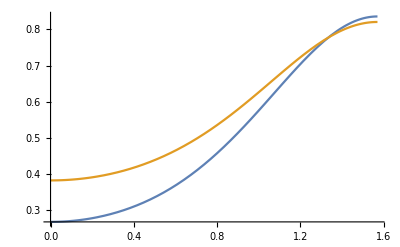

```mathematica
Plot[{NIMS[-2,psi],NIMScorr[-2,psi]/1.6},{psi,0,Pi/2}]
```

```mathematica
fSHRINK[lambda_,theta_]:=1/2*lambda^2*Cos[ArcTan[lambda*Tan[theta]]]^3/Cos[theta]^3
```

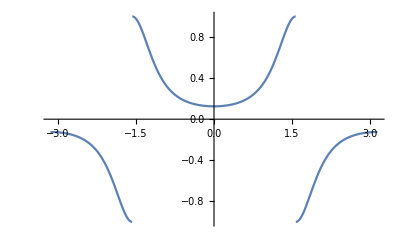

```mathematica
Plot[fSHRINK[.5,theta],{theta,-Pi,Pi}]
```